## Nucleation Analysis (Multi - stranded)

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

PartitionFunctionFILE="PartitionFunction_0_0.out";
dPartitionFunctionFILE="dPartitionFunction_0_0.out";
FreeEnergyFILE="FreeEnergy_0_0.out";
dFreeEnergyFILE="dFreeEnergy_0_0.out";
LambdaFILE="mxd_lambda.out";
RoeFILE="mxd_roe.out";
PotentialDataFILE="POTENTIAL_DATA";
ParametersFILE="Parameters";

CollagenPATH="collagen/results/";
OtherHarmonic1PATH="collagen_anhar1/results/";
OtherHarmonic2PATH="collagen_anhar2/results/";

FrameBox["Numerical Parameters - Harmonic"] // DisplayForm
PartitionFunctionCollagen=Import[CollagenPATH <>PartitionFunctionFILE,"Table"];
dPartitionFunctionCollagen=Import[CollagenPATH <>dPartitionFunctionFILE,"Table"];
FreeEnergyCollagen=Import[CollagenPATH <>FreeEnergyFILE,"Table"];
dFreeEnergyCollagen=Import[CollagenPATH <>dFreeEnergyFILE,"Table"];
PotentialCollagen=Import[CollagenPATH <> PotentialDataFILE,"Table"];
ParametersCollagen=Import[CollagenPATH <>ParametersFILE,"Grid"]
LambdaCollagen=Import[CollagenPATH<>LambdaFILE,"Table"];
RoeCollagen=Import[CollagenPATH<>RoeFILE,"Table"];

FrameBox["Numerical Parameters - Anharmonic 1"] // DisplayForm
PartitionFunctionCollagenAnhar1=Import[OtherHarmonic1PATH<>PartitionFunctionFILE,"Table"];
dPartitionFunctionCollagenAnhar1=Import[OtherHarmonic1PATH<>dPartitionFunctionFILE,"Table"];
FreeEnergyCollagenAnhar1=Import[OtherHarmonic1PATH<>FreeEnergyFILE,"Table"];
dFreeEnergyCollagenAnhar1=Import[OtherHarmonic1PATH<>dFreeEnergyFILE,"Table"];
PotentialCollagenAnhar1=Import[OtherHarmonic1PATH<>PotentialDataFILE,"Table"];
ParametersCollagenAnhar1=Import[OtherHarmonic1PATH<>ParametersFILE,"Grid"]
LambdaCollagenAnhar1=Import[OtherHarmonic1PATH<>LambdaFILE,"Table"];
RoeCollagenAnhar1=Import[OtherHarmonic1PATH<>RoeFILE,"Table"];

FrameBox["Numerical Parameters - Anharmonic 2"] // DisplayForm
PartitionFunctionCollagenAnhar2=Import[OtherHarmonic2PATH<>PartitionFunctionFILE,"Table"];
dPartitionFunctionCollagenAnhar2=Import[OtherHarmonic2PATH<>dPartitionFunctionFILE,"Table"];
FreeEnergyCollagenAnhar2=Import[OtherHarmonic2PATH<>FreeEnergyFILE,"Table"];
dFreeEnergyCollagenAnhar2=Import[OtherHarmonic2PATH<>dFreeEnergyFILE,"Table"];
PotentialCollagenAnhar2=Import[OtherHarmonic2PATH<>PotentialDataFILE,"Table"];
ParametersCollagenAnhar2=Import[OtherHarmonic2PATH<>ParametersFILE,"Grid"]
LambdaCollagenAnhar2=Import[OtherHarmonic2PATH<>LambdaFILE,"Table"];
RoeCollagenAnhar2=Import[OtherHarmonic2PATH<>RoeFILE,"Table"];

L=IntegerPart[ParametersCollagen[[1,2]][[2]]];
m=IntegerPart[ParametersCollagen[[1,3]][[2]]];
n=IntegerPart[ParametersCollagen[[1,4]][[2]]];
kappa=IntegerPart[ParametersCollagen[[1,5]][[2]]];
sigma=IntegerPart[ParametersCollagen[[1,6]][[2]]];

potentialData={PotentialCollagen,PotentialCollagenAnhar1,PotentialCollagenAnhar2};
FreeEnergyData = {FreeEnergyCollagen,FreeEnergyCollagenAnhar1,FreeEnergyCollagenAnhar2};
dFreeEnergyData={dFreeEnergyCollagen,dFreeEnergyCollagenAnhar1,dFreeEnergyCollagenAnhar2};
RoeData={RoeCollagen,RoeCollagenAnhar1,RoeCollagenAnhar2};
LambdaData={LambdaCollagen,LambdaCollagenAnhar1,LambdaCollagenAnhar2};

fsAxesLabel=24;
fs2=16;
fs3=16;

Needs["PlotLegends`"]
```

C:\Users\Hemant\Desktop\CORRECTIONSv1\Results\Collagen\various_potentials\collagen_sim_results

Numerical Parameters - Harmonic

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Numerical Parameters - Anharmonic 1

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Numerical Parameters - Anharmonic 2

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Mean Axial Displacement Analysis (λ''=z+x-2y)

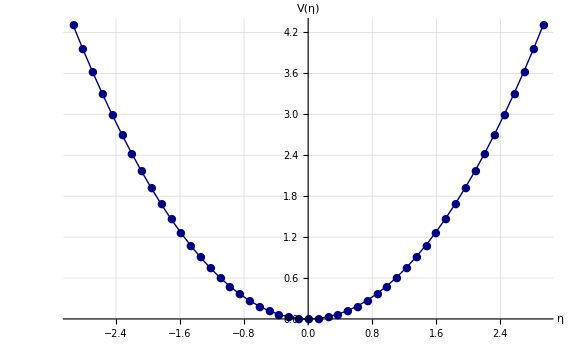
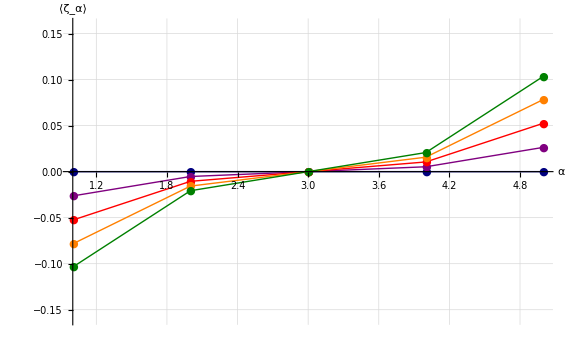

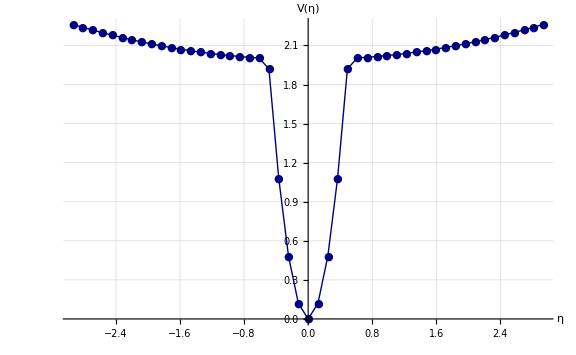
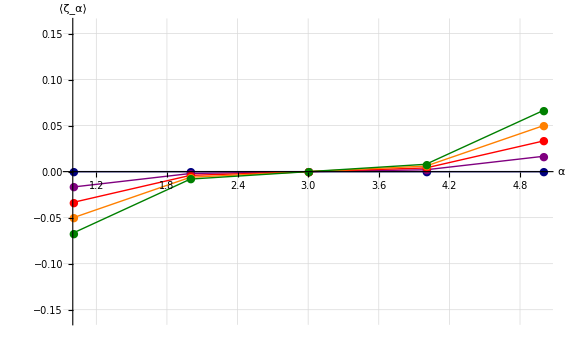

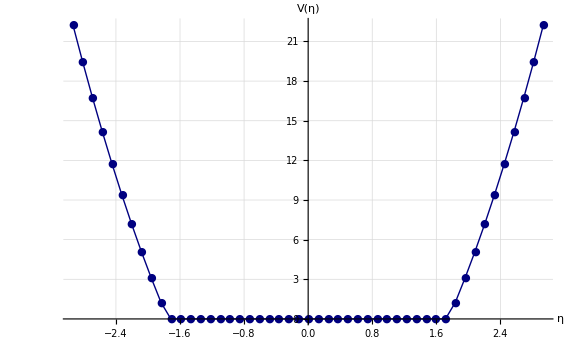
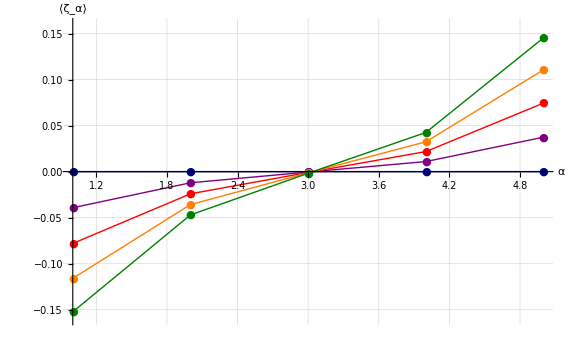

```mathematica
FrameBox["Potential Analysis"] // DisplayForm;

potentialDataPlot=Table[
ListLinePlot[
{
potentialData[[i]]
},
PlotRange->All,
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["η",FontSize->fsAxesLabel],
Style["V(η)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs3},
PlotStyle->{
{Thick,Darker[Blue,0.5]}
},
PlotMarkers->{"●"}
]
,{i,1,3}
];

(*Export["./col_pe_harmonic_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",potentialDataPlot[[1]]];
Export["./col_pe_soft_hard_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",potentialDataPlot[[2]]];
Export["./col_pe_hard_soft_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",potentialDataPlot[[3]]];*)


FrameBox["Mean Axial Displacement Analysis (λ''=z+x-2y)"]//DisplayForm

MXDCollagenDataPlot=Table[
ListLinePlot[
{
-√3 LambdaData[[i]][[1]]+3 RoeData[[i]][[1]],
-√3 LambdaData[[i]][[2]]+3 RoeData[[i]][[2]],
-√3 LambdaData[[i]][[3]]+3 RoeData[[i]][[3]],
-√3 LambdaData[[i]][[4]]+3 RoeData[[i]][[4]],
-√3 LambdaData[[i]][[5]]+3 RoeData[[i]][[5]]
},
PlotRange->{{1,5},{-0.16,0.16}},
AxesOrigin->{1,0},
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["α",FontSize->fsAxesLabel],
Style["⟨ζ_α⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,Darker[Blue,0.5]},
{Thick,Purple},
{Thick,Red},
{Thick,Orange},
{Thick,Darker[Green,0.5]}
},
PlotMarkers->{"●"},
PlotLegend->{
Style["u=0",FontSize->fs3],
Style["u=0.12",FontSize->fs3],
Style["u=0.24",FontSize->fs3],
Style["u=0.36",FontSize->fs3],
Style["u=0.48",FontSize->fs3]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.5,0.4},
LegendPosition->{0.4,-0.6}
]
,{i,1,3}
];

{potentialDataPlot[[1]],MXDCollagenDataPlot[[1]]}
{potentialDataPlot[[2]],MXDCollagenDataPlot[[2]]}
{potentialDataPlot[[3]],MXDCollagenDataPlot[[3]]}
```

```mathematica
Export["./col_mxd_har_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",MXDCollagenDataPlot[[1]]];
Export["./col_mxd_hard_soft_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",MXDCollagenDataPlot[[2]]];
Export["./col_mxd_soft_hard_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",MXDCollagenDataPlot[[3]]];
```